```mathematica
data=Import["~/iCloud/Projects/2022/MachineLearning/Data/5sphere_20dim.csv"]
```

{1}
 |  |  |  |

```mathematica
Dimensions[data]
```

{5800,21}

```mathematica
phi=Table[data[[i,1]],{i,1,Length[data]}];
alpha=Table[Rest[data[[i]]],{i,1,Length[data]}];
```

```mathematica
alpha[[1]]
```

{0,0,0,0.349044,0.265928,0.972677,0.349044,0.265928,0.337739,0,0,0,0,0,0,2.,1.56185,2.,2.,2.}

```mathematica
pcared2=DimensionReduction[alpha,2,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha2=pcared2[alpha]
```

{{-3.61181,0.310406},{-0.406577,3.56938},5796,{1.00732,0.208384},{0.848901,-0.107694}}
 |  |  |  |

```mathematica
rf2=Predict[alpha2->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
Information[rf2]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 0.00472 ± 0.00053
Method | RandomForest
Single evaluation time | 9.44 ms/example
Batch evaluation speed | 8.06 examples/ms
Loss | -3.74 ± 0.038
Model memory | 2.46 MB
Training examples used | 5800 examples
Training time | 1.86 s
 |

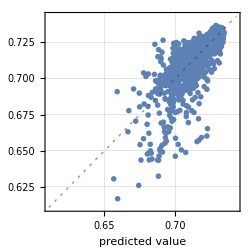
Predictor Measurements
Predictor method | RandomForest
Number of test examples | 5800
Standard deviation | 0.00593 ± 0.0002
Standard deviation baseline | 0.0106 ± 0.00033
R-squared | 0.685 ± 0.029
Mean cross entropy | -3.67 ± 0.022
Single evaluation time | 9.6 ms/example
Batch evaluation speed | 781. examples/s
-Graphics- |

```mathematica
PredictorMeasurements[rf2,alpha2->phi]
```

```mathematica
plotpca2=Table[{alpha2[[i,1]],alpha2[[i,2]],phi[[i]]},{i,1,Length[phi]}]
```

{{-3.61181,0.310406,0.726481},{-0.406577,3.56938,0.720714},5797,{0.848901,-0.107694,0.726612}}
 |  |  |  |

```mathematica
Show[Plot3D[rf2[{x,y}],{x,-15,10},{y,-10,10}],ListPointPlot3D[plotpca2],PlotRange->All]
```

-Graphics3D-

```mathematica
dl2=Predict[alpha2->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
First[dl2]["Model"]["Options"]
```

<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→4,Options→<||>|>,NumberOfParameters→<|Value→7650,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→10,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→0.15,Options→<||>|>|>

```mathematica
5800 0.15
```

870.

```mathematica
First[dl2]["Model"]["Network"]
```

NetGraph[<>]

```mathematica
Show[Plot3D[dl2[{x,y}],{x,-15,10},{y,-10,10}],ListPointPlot3D[plotpca2],PlotRange->All]
```

-Graphics3D-

```mathematica
maxrf1=NMaximize[rf2[{x,y}],{x,y},Method->"NelderMead"]
maxrf2=NMaximize[rf2[{x,y}],{x,y},Method->"RandomSearch"]
maxrf3=NMaximize[rf2[{x,y}],{x,y},Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf2[{x,y}],{x,y},Method->"DifferentialEvolution"]
maxdl1=NMaximize[dl2[{x,y}],{x,y},Method->"NelderMead"]
maxdl2=NMaximize[dl2[{x,y}],{x,y},Method->"RandomSearch"]
maxdl3=NMaximize[dl2[{x,y}],{x,y},Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl2[{x,y}],{x,y},Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733684,{x→0.933181,y→0.670737}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.732417,{x→0.918621,y→0.716689}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.732417,{x→0.918621,y→0.716689}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733789,{x→0.940668,y→0.414981}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729182,{x→0.867657,y→0.38261}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729142,{x→0.921894,y→0.28608}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.728932,{x→0.75721,y→0.152402}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729182,{x→0.867585,y→0.382495}}

```mathematica
maxrf4
```

{0.733789,{x→0.940668,y→0.414981}}

```mathematica
newmax2=pcared2[{0.9406684758473851,0.41498053315859973},"OriginalVectors"]
```

{0.,0.,0.,-0.35827,-0.0409071,0.822792,-0.370235,-0.0109506,0.536837,-0.477266,0.0863396,0.172465,-0.66919,0.220112,-0.119617,2.,1.84733,1.96569,1.98252,1.91145}

```mathematica
ss=newmax2;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-

```mathematica
pcared3=DimensionReduction[alpha,3,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha3=pcared3[alpha]
```

{{-3.61181,0.310406,-1.80701},{-0.406577,3.56938,-2.62313},5797,{0.848901,-0.107694,-0.887219}}
 |  |  |  |

```mathematica
rf3=Predict[alpha3->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
dl3=Predict[alpha3->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
First[dl3]["Model"]["Options"]
```

<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→4,Options→<||>|>,NumberOfParameters→<|Value→7700,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→0.01,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→100,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→0.15,Options→<||>|>|>

```mathematica
vars={x1,x2,x3};
maxrf1=NMaximize[rf3[vars],vars,Method->"NelderMead"]
maxrf2=NMaximize[rf3[vars],vars,Method->"RandomSearch"]
maxrf3=NMaximize[rf3[vars],vars,Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf3[vars],vars,Method->"DifferentialEvolution"]
maxdl1=NMaximize[dl3[vars],vars,Method->"NelderMead"]
maxdl2=NMaximize[dl3[vars],vars,Method->"RandomSearch"]
maxdl3=NMaximize[dl3[vars],vars,Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl3[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.731995,{x1→1.10192,x2→0.233604,x3→0.253109}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730728,{x1→0.990926,x2→0.155494,x3→-0.0590116}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730834,{x1→0.882785,x2→0.395149,x3→0.252838}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.734317,{x1→0.85181,x2→0.41003,x3→-1.47307}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730845,{x1→1.05695,x2→0.470062,x3→-1.14555}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729983,{x1→0.761652,x2→0.0437989,x3→-0.132812}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.73072,{x1→0.984101,x2→0.251376,x3→-0.905347}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730845,{x1→1.05729,x2→0.469505,x3→-1.14566}}

```mathematica
maxrf4
```

{0.734317,{x1→0.85181,x2→0.41003,x3→-1.47307}}

```mathematica
newmax3=pcared3[{0.8518101959746452,0.4100304369014315,-1.473071376063279},"OriginalVectors"]
```

{0.,0.,0.,-0.308417,0.0319618,0.950709,-0.299378,0.0786089,0.708982,-0.395769,0.191318,0.360096,-0.598061,0.32013,0.00652602,2.,1.83427,1.9395,1.981,1.91885}

```mathematica
ss=newmax3;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-

```mathematica
pcared4=DimensionReduction[alpha,4,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha4=pcared4[alpha]
```

{{-3.61181,0.310406,-1.80701,-1.71215},5798,{0.848901,-0.107694,-0.887219,-0.526038}}
 |  |  |  |

```mathematica
rf4=Predict[alpha4->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
dl4=Predict[alpha4->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
First[dl4]["Model"]["Options"]
```

<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→4,Options→<||>|>,NumberOfParameters→<|Value→7750,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→3,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→0.15,Options→<||>|>|>

```mathematica
vars={x1,x2,x3,x4};
maxrf1=NMaximize[rf4[vars],vars,Method->"NelderMead"]
maxrf2=NMaximize[rf4[vars],vars,Method->"RandomSearch"]
maxrf3=NMaximize[rf4[vars],vars,Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf4[vars],vars,Method->"DifferentialEvolution"]
maxdl1=NMaximize[dl4[vars],vars,Method->"NelderMead"]
maxdl2=NMaximize[dl4[vars],vars,Method->"RandomSearch"]
maxdl3=NMaximize[dl4[vars],vars,Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl4[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730623,{x1→1.41799,x2→-0.120541,x3→0.962214,x4→-0.286532}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729039,{x1→0.508509,x2→0.340387,x3→-0.13604,x4→-0.225951}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729778,{x1→1.23583,x2→-0.633735,x3→-0.433305,x4→-0.128216}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.734,{x1→0.714737,x2→0.364359,x3→-0.649699,x4→-0.375443}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730819,{x1→1.05263,x2→0.894945,x3→0.140655,x4→0.34344}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729852,{x1→0.643476,x2→0.766972,x3→0.280303,x4→0.964763}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.7301,{x1→0.76311,x2→1.3026,x3→0.133614,x4→0.580323}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730833,{x1→1.05504,x2→0.898128,x3→0.232972,x4→0.379989}}

```mathematica
maxrf4
```

{0.734,{x1→0.714737,x2→0.364359,x3→-0.649699,x4→-0.375443}}

```mathematica
newmax4=pcared4[{0.7147374771948363,0.3643586901682109,-0.6496985165557059,-0.37544266406845206},"OriginalVectors"]
```

{0.,0.,0.,-0.304873,-0.00987663,0.876307,-0.288821,0.0287788,0.588636,-0.387274,0.138419,0.225635,-0.608225,0.284219,-0.0948632,2.,1.85651,1.98307,1.99659,1.93065}

```mathematica
ss=newmax4;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-

```mathematica
pcared5=DimensionReduction[alpha,5,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha5=pcared5[alpha]
```

{{-3.61181,0.310406,-1.80701,-1.71215,0.76774},5798,{0.848901,-0.107694,-19,-0.526038,0.189944}}
 |  |  |  |

```mathematica
rf5=Predict[alpha5->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
vars={x1,x2,x3,x4,x5};
maxrf1=NMaximize[rf5[vars],vars,Method->"NelderMead"]
maxrf2=NMaximize[rf5[vars],vars,Method->"RandomSearch"]
maxrf3=NMaximize[rf5[vars],vars,Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf5[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733156,{x1→0.815107,x2→0.347633,x3→-0.520628,x4→-0.17264,x5→0.0573674}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.728934,{x1→0.941033,x2→0.839244,x3→0.995193,x4→-0.231281,x5→0.231961}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.728828,{x1→0.974104,x2→0.517816,x3→0.28581,x4→0.39459,x5→-0.442319}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.734,{x1→0.841903,x2→0.203694,x3→-1.51729,x4→-0.492916,x5→0.419215}}

```mathematica
dl5=Predict[alpha5->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
First[dl5]["Model"]["Options"]
```

<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→4,Options→<||>|>,NumberOfParameters→<|Value→7800,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→3,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→0.15,Options→<||>|>|>

```mathematica
maxdl1=NMaximize[dl5[vars],vars,Method->"NelderMead"]
maxdl2=NMaximize[dl5[vars],vars,Method->"RandomSearch"]
maxdl3=NMaximize[dl5[vars],vars,Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl5[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733207,{x1→1.15699,x2→0.222382,x3→-0.656166,x4→-0.478455,x5→-0.65475}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.731485,{x1→0.254053,x2→-0.256609,x3→-0.745211,x4→0.00917006,x5→-1.03235}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.731206,{x1→0.823135,x2→0.921288,x3→-0.8282,x4→-0.997497,x5→0.706198}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733217,{x1→1.10564,x2→0.224635,x3→-0.645697,x4→-0.442682,x5→-0.632879}}

```mathematica
maxrf4
```

{0.734,{x1→0.841903,x2→0.203694,x3→-1.51729,x4→-0.492916,x5→0.419215}}

```mathematica
newmax5=pcared5[{0.8419025859124644,0.2036942437469097,-1.517285079729168,-0.4929161167891048,0.41921490603038725},"OriginalVectors"]
```

{0.,0.,0.,-0.296242,0.0454652,0.944322,-0.272835,0.0947419,0.667378,-0.366113,0.221164,0.321156,-0.567136,0.361928,-0.0144102,2.,1.83834,1.98576,2.01803,1.99822}

```mathematica
ss=newmax5;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-

```mathematica
pcared6=DimensionReduction[alpha,6,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha6=pcared6[alpha]
```

{{-3.61181,0.310406,-1.80701,-1.71215,0.76774,0.778739},5798,{0.848901,-0.107694,3,0.0836389}}
 |  |  |  |

```mathematica
rf6=Predict[alpha6->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
dl6=Predict[alpha6->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
First[dl6]["Model"]["Options"]
```

<|NetworkType→<|Value→FullyConnected,Options→<||>|>,NetworkDepth→<|Value→8,Options→<||>|>,NumberOfParameters→<|Value→17850,Options→<||>|>,ActivationFunction→<|Value→SELU,Options→<||>|>,L2Regularization→<|Value→None,Options→<||>|>,Dropout→<|Value→None,Options→<||>|>,NetInitializationMethod→<|Value→Automatic,Options→<||>|>,OptimizationMethod→<|Value→{ADAM,L2Regularization→None},Options→<||>|>,MaxTrainingRounds→<|Value→3,Options→<||>|>,ValidationSet→<|Value→Automatic,Options→<||>|>,EarlyStopping→<|Value→False,Options→<||>|>,TrainingProgressReporting→<|Value→None,Options→<||>|>,NetTrainOptions→<|Value→{LearningRateMultipliers→{},TargetDevice→CPU},Options→<||>|>,LossFunction→<|Value→Automatic,Options→<||>|>,ValidationSetRatio→<|Value→0.15,Options→<||>|>|>

```mathematica
vars={x1,x2,x3,x4,x5,x6};
maxrf1=NMaximize[rf6[vars],vars,Method->"NelderMead"]
maxrf2=NMaximize[rf6[vars],vars,Method->"RandomSearch"]
maxrf3=NMaximize[rf6[vars],vars,Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf6[vars],vars,Method->"DifferentialEvolution"]
maxdl1=NMaximize[dl6[vars],vars,Method->"NelderMead"]
maxdl2=NMaximize[dl6[vars],vars,Method->"RandomSearch"]
maxdl3=NMaximize[dl6[vars],vars,Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl6[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.731361,{x1→0.79723,x2→0.0910665,x3→0.307441,x4→-0.195168,x5→0.0485925,x6→0.130958}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.7283,{x1→0.483332,x2→-0.0653758,x3→-0.556639,x4→-0.0851508,x5→0.343351,x6→0.0764488}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.727667,{x1→0.813781,x2→-0.00602927,x3→0.40928,x4→-0.149877,x5→0.131702,x6→0.688185}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733472,{x1→0.685165,x2→0.100288,x3→-1.39474,x4→-0.66317,x5→0.470823,x6→-0.0594459}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.732571,{x1→0.223333,x2→-0.0549727,x3→-1.21772,x4→-0.447655,x5→0.306011,x6→0.0724543}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.731343,{x1→0.483332,x2→0.058031,x3→-0.556639,x4→-0.196191,x5→0.343351,x6→-0.306419}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730718,{x1→0.350743,x2→-0.215872,x3→0.573723,x4→0.0193329,x5→-0.162311,x6→0.129477}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.732553,{x1→0.242029,x2→-0.0782899,x3→-1.27184,x4→-0.479988,x5→0.294942,x6→0.012357}}

```mathematica
maxrf4
```

{0.733472,{x1→0.685165,x2→0.100288,x3→-1.39474,x4→-0.66317,x5→0.470823,x6→-0.0594459}}

```mathematica
newmax6=pcared6[{0.6851645560625329,0.10028825608742836,-1.3947419379979695,-0.663169540038592,0.47082304020943316,-0.05944594729362526},"OriginalVectors"]
```

{0.,0.,0.,-0.281563,0.0457976,0.917011,-0.25276,0.096006,0.627066,-0.343894,0.222802,0.282793,-0.545959,0.364466,-0.0363487,2.,1.84765,1.99449,2.01462,2.01189}

```mathematica
ss=newmax6;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-

```mathematica
pcared8=DimensionReduction[alpha,8,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha8=pcared8[alpha]
```

{{-3.61181,0.310406,-1.80701,-1.71215,0.76774,0.778739,0.245328,-0.237625},{1},5796,{1},{1}}
 |  |  |  |

```mathematica
rf8=Predict[alpha8->phi,Method->"RandomForest",PerformanceGoal->"Quality"]
dl8=Predict[alpha8->phi,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
vars={x1,x2,x3,x4,x5,x6,x7,x8};
maxrf1=NMaximize[rf8[vars],vars,Method->"NelderMead"]
maxrf2=NMaximize[rf8[vars],vars,Method->"RandomSearch"]
maxrf3=NMaximize[rf8[vars],vars,Method->"SimulatedAnnealing"]
maxrf4=NMaximize[rf8[vars],vars,Method->"DifferentialEvolution"]
maxdl1=NMaximize[dl8[vars],vars,Method->"NelderMead"]
maxdl2=NMaximize[dl8[vars],vars,Method->"RandomSearch"]
maxdl3=NMaximize[dl8[vars],vars,Method->"SimulatedAnnealing"]
maxdl4=NMaximize[dl8[vars],vars,Method->"DifferentialEvolution"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.727667,{x1→0.290578,x2→0.113452,x3→0.166168,x4→0.322266,x5→0.00382895,x6→0.0519154,x7→0.169548,x8→-0.101873}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729884,{x1→0.791005,x2→0.511939,x3→-0.397084,x4→-0.0653723,x5→0.252773,x6→0.211933,x7→-0.148279,x8→-0.0826807}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.727139,{x1→1.51489,x2→-0.305164,x3→-0.814265,x4→-2.02143,x5→0.718481,x6→0.00190976,x7→0.12232,x8→-0.143617}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.733895,{x1→0.652399,x2→-0.19796,x3→-1.59736,x4→-0.68201,x5→0.435911,x6→-0.0434491,x7→-0.328562,x8→-0.210445}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.730589,{x1→1.1074,x2→0.429994,x3→-0.64291,x4→0.383798,x5→0.551976,x6→0.788768,x7→-0.0326196,x8→-0.416665}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729428,{x1→0.924638,x2→-0.656392,x3→-0.176155,x4→-0.337141,x5→0.668356,x6→-0.412413,x7→-0.200064,x8→0.00330235}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.729734,{x1→-0.135658,x2→0.668948,x3→-0.843878,x4→-0.166156,x5→0.531411,x6→-0.431093,x7→-1.29119,x8→0.0569852}}

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x1,x2,x3,x4,x5,x6,x7,x8}).

General::stop: Further output of PredictorFunction::mlincfttp will be suppressed during this calculation.

{0.73265,{x1→3.76155,x2→2.79251,x3→-1.77799,x4→-2.71783,x5→-2.42003,x6→-0.0638751,x7→-2.70833,x8→-1.56939}}

```mathematica
maxrf4
```

{0.733895,{x1→0.652399,x2→-0.19796,x3→-1.59736,x4→-0.68201,x5→0.435911,x6→-0.0434491,x7→-0.328562,x8→-0.210445}}

```mathematica
newmax8=pcared8[{0.6523990110303972,-0.19796016312915088,-1.5973603963441587,-0.6820104526867652,0.4359110286075991,-0.04344910741128295,-0.32856238604100557,-0.2104452220117936},"OriginalVectors"]
```

{0.,0.,0.,-0.28008,0.0612879,0.904846,-0.247552,0.132203,0.617726,-0.337275,0.280584,0.272518,-0.531069,0.429312,-0.0207041,2.,1.80838,2.0566,1.99087,1.99718}

```mathematica
ss=newmax8;
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]}]
```

-Graphics3D-